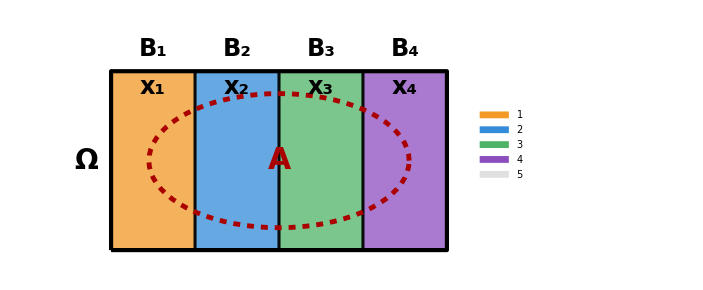
f
-Graphics-f · χ_A
-Graphics-

```mathematica
ClearAll[x, y, nB, cortes, centros, cenA, semA, limY, colB, colAc, enA, subInd, marco, piezas,
  panelIzq, panelDer, tituloIzq, tituloDer, leyenda, diagrama];

nB = 4;
cortes = {0, 2, 4, 6, 8};              (* cortes de las bandas B_i *)
centros = {1.45, 3, 5, 6.55};          (* centro de cada pieza B_i ∩ A *)
limY = 4;
cenA = {4, 2}; semA = {3.1, 1.5};      (* A: elipse que corta a las cuatro bandas *)

colB = {RGBColor[0.95, 0.6, 0.15], RGBColor[0.2, 0.55, 0.85],
   RGBColor[0.3, 0.7, 0.4], RGBColor[0.55, 0.3, 0.75]};
colAc = GrayLevel[0.88];               (* A^c *)

enA = ((x - cenA[[1]])/semA[[1]])^2 + ((y - cenA[[2]])/semA[[2]])^2 < 1;
subInd[k_Integer] := FromCharacterCode[8320 + k];

marco = {FaceForm[None], EdgeForm[{Black, AbsoluteThickness[3]}], Rectangle[{0, 0}, {8, limY}]};

(* ---------- izquierda: f, con la partición {B_i} de Ω y el conjunto A ---------- *)
panelIzq = Graphics[{
    Table[{colB[[i]], Opacity[0.75], EdgeForm[{Black, AbsoluteThickness[2]}],
      Rectangle[{cortes[[i]], 0}, {cortes[[i + 1]], limY}]}, {i, 1, nB}],
    {Darker[Red], Dashed, AbsoluteThickness[3.5], Circle[cenA, semA]},
    marco,
    {Black,
     Table[Text[Style["B" <> subInd[i], 24, Bold],
       {(cortes[[i]] + cortes[[i + 1]])/2, limY + 0.5}], {i, 1, nB}],
     Table[Text[Style["x" <> subInd[i], 24, Bold],
       {(cortes[[i]] + cortes[[i + 1]])/2, 3.65}], {i, 1, nB}],
     Text[Style["A", 30, Bold, Darker[Red]], cenA],
     Text[Style["Ω", 28, Bold], {-0.6, limY/2}]}},
   PlotRange -> {{-1.2, 8.3}, {-0.3, 5.0}}, ImageSize -> 520];

(* ---------- derecha: f·χ_A, con la partición {B_i ∩ A} ∪ {A^c} ---------- *)
piezas = Table[
   RegionPlot[Evaluate[cortes[[i]] ≤ x < cortes[[i + 1]] && enA], {x, 0, 8}, {y, 0, limY},
    PlotStyle -> Directive[colB[[i]], Opacity[0.75]],
    BoundaryStyle -> Directive[Black, AbsoluteThickness[2]],
    PlotPoints -> 80, MaxRecursion -> 3],
   {i, 1, nB}];

panelDer = Show[
   Graphics[{colAc, Rectangle[{0, 0}, {8, limY}]}],
   Sequence @@ piezas,
   Graphics[{
     {Black, AbsoluteThickness[2.5], Circle[cenA, semA]},
     marco,
     {Black,
      Table[Text[Style["x" <> subInd[i], 24, Bold], {centros[[i]], 2}], {i, 1, nB}],
      Table[Text[Style["0", 24, Bold, GrayLevel[0.35]], p],
       {p, {{0.45, 3.45}, {7.55, 3.45}, {0.45, 0.55}, {7.55, 0.55}}}],
      Text[Style["Ω", 28, Bold], {-0.6, limY/2}]}}],
   PlotRange -> {{-1.2, 8.3}, {-0.3, 5.0}}, AspectRatio -> Automatic,
   Frame -> False, Axes -> False, ImageSize -> 520];

tituloIzq = Style["f", 26, Bold];
tituloDer = Style[Row[{"f · ", Subscript["χ", "A"]}], 26, Bold];

leyenda = SwatchLegend[Append[colB, colAc],
   Append[Table["B" <> subInd[i] <> "∩A", {i, 1, nB}], "Aᶜ"],
   LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20];

diagrama = Legended[
   Row[{Column[{tituloIzq, panelIzq}, Alignment -> Center, Spacings -> 0.4], Spacer[30],
     Column[{tituloDer, panelDer}, Alignment -> Center, Spacings -> 0.4]}],
   leyenda];

diagrama

Export[CloudObject["T3_P54_b"], diagrama,"PNG", Background -> None,ImageResolution ->300];
```

```mathematica
ClearAll[nB, cortes, alto, offR, colB, subInd, fMap, xe, ys, tiraIzq, tiraDer, marco, midIzq, midDer,
  omega1, imagen1, panelIzq, panelDer, flechas, puntos, titulos, grafico, leyenda, diagrama];

nB = 4;
cortes = {0, 2, 4, 6, 8};   (* cortes de las bandas B_i en Ω₂ *)
alto = 4;
offR = 14;                  (* desplazamiento horizontal del panel de Ω₂ *)

colB = {RGBColor[0.95, 0.6, 0.15], RGBColor[0.2, 0.55, 0.85],
   RGBColor[0.3, 0.7, 0.4], RGBColor[0.55, 0.3, 0.75]};

subInd[k_Integer] := FromCharacterCode[8320 + k];

(* una aplicación f : Ω₁ -> Ω₂ de ejemplo; solo sirve para que las antiimágenes salgan curvas *)
fMap[x_, y_] := 0.6 + 0.85 x + 0.5 Sin[1.6 y];

(* frontera de la antiimagen del corte c, es decir, los puntos (x,y) con f(x,y) = c *)
xe[c_, y_] := Clip[(c - 0.6 - 0.5 Sin[1.6 y])/0.85, {0, 8}];

ys = Range[0, alto, 0.05];

(* antiimagen f⁻.b9(B_i): la franja entre las curvas de nivel de los cortes c_i y c_{i+1} *)
tiraIzq[i_] := Polygon[Join[
    Table[{xe[cortes[[i]], y], y}, {y, ys}],
    Table[{xe[cortes[[i + 1]], y], y}, {y, Reverse[ys]}]]];

tiraDer[i_] := Rectangle[{offR + cortes[[i]], 0}, {offR + cortes[[i + 1]], alto}];

marco[x0_] := {FaceForm[None], EdgeForm[{Black, AbsoluteThickness[3]}],
   Rectangle[{x0, 0}, {x0 + 8, alto}]};

(* centro de cada franja a la altura y, para colocar las etiquetas *)
midIzq[i_, y_] := (xe[cortes[[i]], y] + xe[cortes[[i + 1]], y])/2;
midDer[i_] := offR + (cortes[[i]] + cortes[[i + 1]])/2;

(* ---------- izquierda: Ω₁ con la partición {f⁻.b9(B_i)}, donde g∘f vale x_i ---------- *)
panelIzq = {
   Table[{colB[[i]], Opacity[0.75], EdgeForm[{Black, AbsoluteThickness[2]}], tiraIzq[i]}, {i, 1, nB}],
   marco[0],
   {Black,
    Table[Text[Style["f⁻.b9(B" <> subInd[i] <> ")", 18, Bold],
      {midIzq[i, alto], alto + 0.5}], {i, 1, nB}],
    Table[Text[Style["x" <> subInd[i], 24, Bold], {midIzq[i, 1.5], 1.5}], {i, 1, nB}],
    Text[Style["Ω₁", 28, Bold], {-1.1, alto/2}]}};

(* ---------- derecha: Ω₂ con la partición {B_i}, donde g vale x_i ---------- *)
panelDer = {
   Table[{colB[[i]], Opacity[0.75], EdgeForm[{Black, AbsoluteThickness[2]}], tiraDer[i]}, {i, 1, nB}],
   marco[offR],
   {Black,
    Table[Text[Style["B" <> subInd[i], 24, Bold], {midDer[i], alto + 0.5}], {i, 1, nB}],
    Table[Text[Style["x" <> subInd[i], 24, Bold], {midDer[i], 1.5}], {i, 1, nB}],
    Text[Style["Ω₂", 28, Bold], {offR - 1.1, alto/2}]}};

(* ---------- las flechas f y f⁻.b9 entre los dos paneles ---------- *)
flechas = {
   {Black, AbsoluteThickness[4], Arrowheads[0.03], Arrow[{{8.9, 3.5}, {13.1, 3.5}}]},
   {Black, AbsoluteThickness[4], Arrowheads[0.03], Arrow[{{13.1, 0.7}, {8.9, 0.7}}]},
   Text[Style["f", 28, Bold], {11, 4.15}],
   Text[Style["f⁻.b9", 28, Bold], {11, 0.05}]};

(* ---------- un punto ω₁ y su imagen f(ω₁): (g∘f)(ω₁) = g(f(ω₁)) ---------- *)
omega1 = {5.2, 2.8};
imagen1 = {offR + fMap @@ omega1, 2.8};

puntos = {
   {Darker[Red], Dashed, AbsoluteThickness[2.5], Arrowheads[0.02], Arrow[{omega1, imagen1}]},
   {Black, EdgeForm[{White, AbsoluteThickness[1.5]}], Disk[omega1, 0.14], Disk[imagen1, 0.14]},
   {Black,
    Text[Style["ω₁", 22, Bold], omega1 + {-0.5, 0.45}],
    Text[Style["f(ω₁)", 22, Bold], imagen1 + {0, 0.55}]}};

titulos = {Black,
   Text[Style["g ∘ f", 30, Bold], {4, alto + 1.7}],
   Text[Style["g", 30, Bold], {offR + 4, alto + 1.7}]};

grafico = Graphics[{panelIzq, panelDer, flechas, puntos, titulos},
   PlotRange -> {{-2.6, offR + 9.4}, {-0.9, alto + 2.5}}, ImageSize -> 1100];

leyenda = SwatchLegend[Append[colB, Darker[Red]],
   Append[Table["B" <> subInd[i] <> "  ↔  f⁻.b9(B" <> subInd[i] <> ")", {i, 1, nB}],
    "ω₁  →  f(ω₁)"],
   LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20];

diagrama = Legended[grafico, leyenda];

diagrama

Export[CloudObject["T3_P55"], diagrama,"PNG", Background -> None,ImageResolution -> 300];
```

-Graphics-

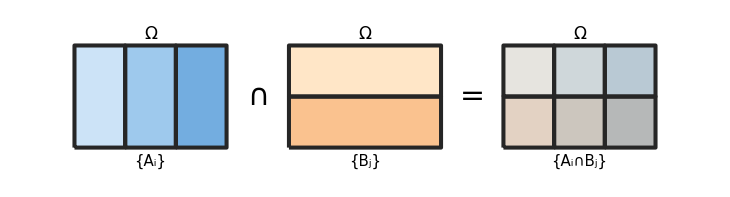

```mathematica
(* Diagrama: refinamiento común de las particiones {A_i} y {B_j} *)

n = 3;  m = 2;            (* número de conjuntos en cada partición *)
w = 1.3;  h = 1.3;        (* ancho de cada franja A_i, alto de cada franja B_j *)
ancho = n w;  alto = m h;
sep = 1.6;                (* separación entre paneles *)
x0A = 0;  x0B = ancho + sep;  x0C = 2 (ancho + sep);

(* Colores *)
colA = {RGBColor[0.80, 0.89, 0.97], RGBColor[0.62, 0.79, 0.93], RGBColor[0.45, 0.68, 0.88]};
colB = {RGBColor[1.00, 0.90, 0.78], RGBColor[0.98, 0.76, 0.56]};
borde = EdgeForm[{GrayLevel[0.15], Thickness[0.004]}];

(* Etiquetas *)
etA[i_] := Subscript[Style["A", Italic], i];
etB[j_] := Subscript[Style["B", Italic], j];
etAB[i_, j_] := Style[Row[{etA[i], "∩", etB[j]}], 11];

(* Panel 1: partición {A_i} (franjas verticales) *)
panelA = Table[
   {borde, colA[[i]],
    Rectangle[{x0A + (i - 1) w, 0}, {x0A + i w, alto}],
    Text[Style[etA[i], 15], {x0A + (i - 1/2) w, alto/2}]},
   {i, n}];

(* Panel 2: partición {B_j} (franjas horizontales) *)
panelB = Table[
   {borde, colB[[j]],
    Rectangle[{x0B, alto - j h}, {x0B + ancho, alto - (j - 1) h}],
    Text[Style[etB[j], 15], {x0B + ancho/2, alto - (j - 1/2) h}]},
   {j, m}];

(* Panel 3: partición común {A_i ∩ B_j} *)
panelC = Table[
   {borde, Blend[{colA[[i]], colB[[j]]}],
    Rectangle[{x0C + (i - 1) w, alto - j h}, {x0C + i w, alto - (j - 1) h}],
    Text[etAB[i, j], {x0C + (i - 1/2) w, alto - (j - 1/2) h}]},
   {i, n}, {j, m}];

(* Símbolos entre paneles *)
simbolos = {
   Text[Style["∩", 30], {x0A + ancho + sep/2, alto/2}],
   Text[Style["=", 30], {x0B + ancho + sep/2, alto/2}]};

(* Etiquetas Ω (arriba) y nombres de las particiones (abajo) *)
omegas = Table[
   Text[Style["Ω", 17, Italic], {x0 + ancho/2, alto + 0.3}],
   {x0, {x0A, x0B, x0C}}];

pies = {
   Text[Style[Row[{"{", etA["i"], "}"}], 15], {x0A + ancho/2, -0.35}],
   Text[Style[Row[{"{", etB["j"], "}"}], 15], {x0B + ancho/2, -0.35}],
   Text[Style[Row[{"{", etA["i"], "∩", etB["j"], "}"}], 15],
    {x0C + ancho/2, -0.35}]};

diagrama = Graphics[
   {panelA, panelB, panelC, simbolos, omegas, pies},
   PlotRange -> {{-0.2, x0C + ancho + 0.2}, {-0.8, alto + 0.7}}];

diagrama

Export[CloudObject["T3_P56.png"], diagrama, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700];
```

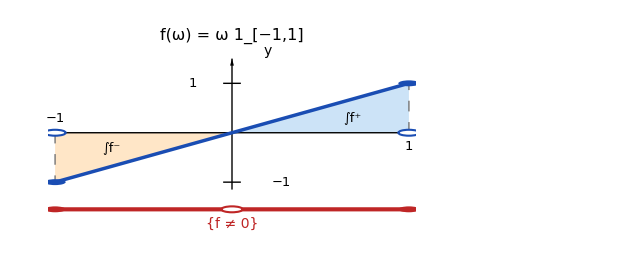

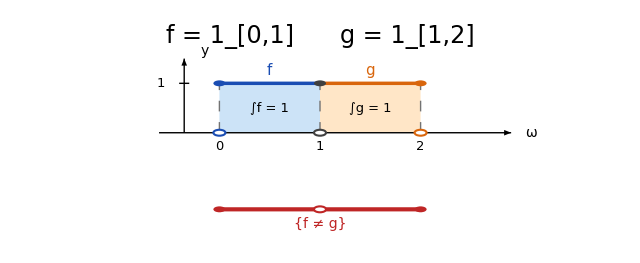

```mathematica
(* Diagrama: integrales iguales pero funciones distintas *)

colF    = RGBColor[0.10, 0.30, 0.70];   (* f *)
colFc   = RGBColor[0.80, 0.89, 0.97];   (* relleno claro de f / f^+ *)
colG    = RGBColor[0.85, 0.40, 0.05];   (* g *)
colGc   = RGBColor[1.00, 0.90, 0.78];   (* relleno claro de g / f^- *)
colRojo = RGBColor[0.75, 0.15, 0.15];   (* conjunto donde f != 0 o f != g *)
r  = 0.06;                              (* radio de los puntos *)
yM = -1.55;                             (* altura de la marca del conjunto *)

(* Punto cerrado (valor tomado) o abierto (valor no tomado) *)
punto[{x_, y_}, col_, cerrado_] :=
  If[cerrado,
   {col, Disk[{x, y}, r]},
   {White, Disk[{x, y}, r], col, AbsoluteThickness[1.5], Circle[{x, y}, r]}];

(* ---------- Panel 1: f(w) = w 1_[-1,1], con integral 0 ---------- *)
panel1 = Graphics[{
    EdgeForm[None],
    (* regiones de f^+ y f^- *)
    colFc, Polygon[{{0, 0}, {1, 0}, {1, 1}}],
    colGc, Polygon[{{-1, 0}, {0, 0}, {-1, -1}}],

    (* guías en los saltos *)
    GrayLevel[0.45], AbsoluteThickness[1], Dashing[{0.012, 0.012}],
    Line[{{1, 0}, {1, 1}}], Line[{{-1, 0}, {-1, -1}}],
    Dashing[{}],

    (* ejes y marcas *)
    Black, AbsoluteThickness[1], Arrowheads[0.03],
    Arrow[{{-2.3, 0}, {2.3, 0}}],
    Arrow[{{0, -1.15}, {0, 1.5}}],
    Line[{{1, -0.05}, {1, 0.05}}], Line[{{-1, -0.05}, {-1, 0.05}}],
    Line[{{-0.05, 1}, {0.05, 1}}], Line[{{-0.05, -1}, {0.05, -1}}],
    Text[Style["1", 13], {1, -0.28}],
    Text[Style["−1", 13], {-1, 0.28}],
    Text[Style["1", 13], {-0.22, 1}],
    Text[Style["−1", 13], {0.28, -1}],
    Text[Style["ω", Italic, 14], {2.5, 0}],
    Text[Style["y", Italic, 14], {0.2, 1.65}],

    (* gráfica de f y sus puntos *)
    colF, AbsoluteThickness[2.5], Line[{{-1, -1}, {1, 1}}],
    punto[{1, 1}, colF, True], punto[{-1, -1}, colF, True],
    punto[{1, 0}, colF, False], punto[{-1, 0}, colF, False],

    (* etiquetas de las regiones *)
    Black,
    Text[Style[Row[{"∫", Superscript[Style["f", Italic], "+"]}], 13],
     {0.68, 0.3}],
    Text[Style[Row[{"∫", Superscript[Style["f", Italic], "−"]}], 13],
     {-0.68, -0.3}],

    (* conjunto {f != 0} = [-1,1] \ {0} *)
    colRojo, AbsoluteThickness[3], Line[{{-1, yM}, {1, yM}}],
    punto[{-1, yM}, colRojo, True], punto[{1, yM}, colRojo, True],
    punto[{0, yM}, colRojo, False],
    Text[Style[Row[{"{", Style["f", Italic], " ≠ 0}"}], 14, colRojo],
     {0, yM - 0.3}],

    (* título *)
    Black,
    Text[Style[Row[{Style["f", Italic], "(", Style["ω", Italic], ") = ",
        Style["ω", Italic], " ",
        Subscript[Style["1", Bold], Row[{"[", "−1", ",", "1", "]"}]]}], 16],
     {0, 1.95}]
    },
   PlotRange -> {{-1, 1}, {-2.15, 2.2}}];

(* ---------- Panel 2: f = 1_[0,1], g = 1_[1,2], ambas con integral 1 ---------- *)
panel2 = Graphics[{
    EdgeForm[None],
    (* regiones bajo f y bajo g *)
    colFc, Rectangle[{0, 0}, {1, 1}],
    colGc, Rectangle[{1, 0}, {2, 1}],

    (* guías en los saltos *)
    GrayLevel[0.45], AbsoluteThickness[1], Dashing[{0.012, 0.012}],
    Line[{{0, 0}, {0, 1}}], Line[{{1, 0}, {1, 1}}], Line[{{2, 0}, {2, 1}}],
    Dashing[{}],

    (* ejes y marcas *)
    Black, AbsoluteThickness[1], Arrowheads[0.03],
    Arrow[{{-0.6, 0}, {2.9, 0}}],
    Arrow[{{-0.35, 0}, {-0.35, 1.5}}],
    Table[{Line[{{x, -0.05}, {x, 0.05}}], Text[Style[x, 13], {x, -0.28}]},
     {x, 0, 2}],
    Line[{{-0.40, 1}, {-0.30, 1}}], Text[Style["1", 13], {-0.58, 1}],
    Text[Style["ω", Italic, 14], {3.1, 0}],
    Text[Style["y", Italic, 14], {-0.15, 1.65}],

    (* gráficas de f y g *)
    colF, AbsoluteThickness[2.5], Line[{{0, 1}, {1, 1}}],
    colG, Line[{{1, 1}, {2, 1}}],
    punto[{0, 1}, colF, True], punto[{0, 0}, colF, False],
    punto[{2, 1}, colG, True], punto[{2, 0}, colG, False],
    (* punto común en w = 1: f(1) = g(1) = 1 *)
    punto[{1, 1}, GrayLevel[0.25], True],
    punto[{1, 0}, GrayLevel[0.25], False],

    (* etiquetas *)
    Text[Style[Style["f", Italic], 15, colF], {0.5, 1.25}],
    Text[Style[Style["g", Italic], 15, colG], {1.5, 1.25}],
    Black,
    Text[Style[Row[{"∫", Style["f", Italic], " = 1"}], 13], {0.5, 0.5}],
    Text[Style[Row[{"∫", Style["g", Italic], " = 1"}], 13], {1.5, 0.5}],

    (* conjunto {f != g} = [0,1) U (1,2] *)
    colRojo, AbsoluteThickness[3], Line[{{0, yM}, {2, yM}}],
    punto[{0, yM}, colRojo, True], punto[{2, yM}, colRojo, True],
    punto[{1, yM}, colRojo, False],
    Text[Style[Row[{"{", Style["f", Italic], " ≠ ", Style["g", Italic], "}"}],
      14, colRojo], {1, yM - 0.3}],

    (* título *)
    Black,
    Text[Style[Row[{
        Style[Row[{Style["f", Italic], " = ",
           Subscript[Style["1", Bold], Row[{"[", "0", ",", "1", "]"}]]}], colF],
        "      ",
        Style[Row[{Style["g", Italic], " = ",
           Subscript[Style["1", Bold], Row[{"[", "1", ",", "2", "]"}]]}], colG]}], 24],
     {1, 1.95}]
    },
   PlotRange -> {{-1.6, 3.6}, {-2.15, 2.2}}];

panel1
panel2
```

```mathematica
Export[CloudObject["T3_P58_a.png"], panel1, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 900];
Export[CloudObject["T3_P58_b.png"], panel2, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 900];
```